```mathematica
摆角不同,周期也不同,观察“失步”现象
```

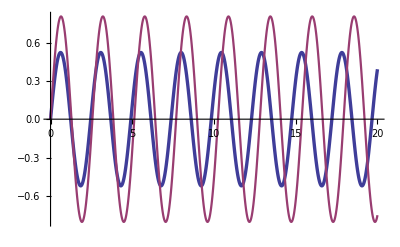

```mathematica
g=9.8;L=1.5;Ω=√(g/L);
v01=0.2;ω01=v01/L;
v02=3;ω02=v02/L;
ss=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],
θ[0]==0,θ'[0]==ω01},θ,{t,0,20}];
θ1=θ/.ss[[1]];
bs=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],
θ[0]==0,θ'[0]==ω02},θ,{t,0,20}];
θ2=θ/.bs[[1]];
Plot[{10*θ1[t],θ2[t]},{t,0,20},
PlotStyle->{Thickness[0.006],Thickness[0.004]},
AxesStyle->Thickness[0.003]]
Clear[g,L,Ω,v01,v02,ω01,ω02,ss,bs,θ1,θ2]
```